SciDraw examples: Diagrams

M. A. Caprio, Department of Physics, University of Notre Dame
rev. February 20, 2014

## Package initialization

If you have not already loaded the SciDraw package since starting this Mathematica session, you must do so now.  See the user guide for information first on installing the package and then on loading it at the beginning of each Mathematica session.

```mathematica
Get["SciDraw`"];
```

𝒮𝒸𝒾𝒟𝓇𝒶𝓌: Publication–quality scientific figures with Mathematica
M. A. Caprio, University of Notre Dame
Version 0.0.0 (November 24, 2013)
View color paletteVisit home page  -Graphics-

## Using anchors, FigBracket, and FigArrow -- Schematic diagram of a projectile’s trajectory

```mathematica
Figure[
FigurePanel[
{

SetOptions[FigObject,FontSize->15];

(* trajectory *)
FigLine⟦"trajectory"⟧[
Plot[{2-x^2},{x,-1,1},PlotPoints->2],
LineThickness->1.5
];
FigCircle⟦"projectile"⟧[FigAnchor["trajectory",Center,0.15],Radius->Canvas[10],FillColor->Gray];

(* arrows *)
ScopeOptions[
SetOptions[FigArrow,ArrowType->Block,Width->3,FillColor->None];
FigArrow⟦"arrow1"⟧[{
AlongAnchor[FigAnchor["trajectory",Tail],-20],
AlongAnchor[FigAnchor["trajectory",Tail],-5]
}];
FigArrow⟦"arrow2"⟧[{
AlongAnchor[FigAnchor["trajectory",Head],+5],
AlongAnchor[FigAnchor["trajectory",Head],+20]
}];
];

(* origin point *)
FigAnchor⟦"origin"⟧[{0,0}];
FigPoint["origin",PointSize->5];

(* connector lines *)
ScopeOptions[
SetOptions[FigLine,LineDashing->3];
FigLine⟦"line1"⟧[{FigAnchor["origin"],FigAnchor["trajectory",Tail]}];
FigLine⟦"line2"⟧[{FigAnchor["origin"],FigAnchor["trajectory",Head]}];
];

(* angle marker *)
FigCircle⟦"arc"⟧[
"origin",
AngleRange->{FigAnchor["trajectory",Tail],FigAnchor["trajectory",Head]},
Radius->Canvas[30],ShowFill->False,ShowHead->True
];
FigLabel[FigAnchor["arc",Tangent,{"Angle",Pi/2}],"Δθ",TextOffset->{0,0},TextBackground->Automatic];

(* height brackets *)
SetOptions[FigBracket,BracketTextOffset->{0,0},BracketTextBackground->Automatic,BracketTextMargin->2],
FigBracket[Left,Scaled[0.10],{"origin",FigAnchor["trajectory",Center,0.5]},BracketLabel->Subscript[textit["y"],"max"]],
FigBracket[Left,Scaled[0.17],{"origin",FigAnchor["projectile",Center]},BracketLabel->Row[{textit["y"],"(",textit["t"],")"}]];

FigRectangle[
AdjustRegion[
BoundingRegion[{"origin","trajectory","arrow1","arrow2"}],
RegionExtension->Scaled[0.03]
],LineColor->Gray,FillColor->None
],

(* anchors -- uncomment these to see some anchors *)
(*
FigAnchorMarker[FigAnchor["origin"]];
FigAnchorMarker[FigAnchor["line1",Tail]];
FigAnchorMarker[FigAnchor["line2",Tail]];
FigAnchorMarker[FigAnchor["trajectory",Tail]];
FigAnchorMarker[FigAnchor["trajectory",Head]];
FigAnchorMarker[FigAnchor["projectile",Center]];
*)

},
PlotRange->{{-2,1.5},{-0.5,2.5}},Background->Moccasin,PanelLetter->"(a)",Ticks->None
]
]
```

-Graphics-

## Diagram with various special arrow types

Note the uses of "Squiggle" and "DoubleLine" arrows

```mathematica
Figure[
FigurePanel[
{

(* target *)
FigRectangle[{0,0},Radius->{0.03,0.3},FillColor->Gold];

(* beam *)
ScopeOptions[
SetOptions[FigArrow,ArrowType->"DoubleLine",Width->3,FillColor->Gray];
FigArrow[{{-2,0},{0,0}},ShowHead->False,HeadLength->0];
FigArrow[{{0,0},{2,0}},ShowFill->False];
];

(* gamma rays *)
ScopeOptions[
SetOptions[FigArrow,ArrowType->"Squiggle"];
FigArrow[{{0,0},{1,1}},Color->Blue,SquiggleWavelength->7];
FigArrow[{{0,0},{-1,-1}},Color->Red,SquiggleWavelength->13];
];

(* arc indicating angle *)
FigCircle[
{0,0},
Radius->0.3,AngleRange->{0,Pi/4},
ShowFill->False,
TangentLabel->"φ",TextOrientation->Horizontal,TextOffset->Left,TextBuffer->3
];

},
PlotRange->{{-2,2},{-1,1}},
Frame->False
],
CanvasSize->{4,2},
CanvasMargin->0
]
```

-Graphics-

## Spline, axis, using anchors for labeling, and the “predefined labels” for a curve -- A basic demonstration

```mathematica
Module[
{pts={{1,1},{2,3},{3,-1},{4,+1},{5,0}}},
Figure[
FigurePanel[
{

(* spline curve *)
FigBSpline⟦"curve"⟧[
pts,
ShowHead->True,LineThickness->2,
LeftLabel->"Left",LeftLabelPosition->0.25,
RightLabel->"Right",RightLabelPosition->0.25,
CenterLabel->"Center",CenterLabelPosition->0.75,CenterTextBackground->Automatic,
HeadLabel->"Head"
];

(* dot at tail *)
FigPoint[FigAnchor["curve",Tail],PointSize->10],

(* label pointing to spline curve *)
FigLabel⟦"label"⟧[
Scaled[{0.75,0.75}],
StackText[Center,0,{"Spline","curve"}],
FontSize->18,TextFrame->True,TextMargin->4,TextRoundingRadius->2
];
FigArrow⟦"arrow"⟧[{FigAnchor["label",Left,-0.5],FigAnchor["curve",Center,0.5]},HeadRecess->10];

(* commentary *)
FigLine[
{FromHead[Canvas[{+30,+5}]],FigAnchor["arrow",Center,0.9]},
LineDashing->2,
TailLabel->StackText[Left,0.3,{"Note use of",texttt["HeadRecess"]}],
TextOrientation->Horizontal,TailTextOffset->Left,
TextMargin->2,
FontSize->8
];

(* standalone axis *)
FigAxis[Left,Scaled[0.1],{-1,3},Ticks->Automatic,AxisLabel->textit[y]]
},
PlotRange->{{0,6},{-2,4}},
Ticks->None,
Background->Moccasin
]
]
]
```

-Graphics-

## Using arrows to connect objects -- Hierarchy chart or flow chart

Figure concept from M. Morrison

```mathematica
(* set a style for the chart components -- this could be shared across many figures *)
DefineStyle["chart",
{
FigObject->{FontFamily->"Comic Sans MS",FontSize->12,FillColor->Moccasin},
FigLabel->{TextRoundingRadius->2,TextBackground->Moccasin,TextFrame->True,TextMargin->2},
FigArrow->{LineColor->Firebrick,ShowHead->True}
}
];

(* generate figure *)
Figure[
{
FigurePanel[
{
FigLabel⟦"content"⟧[{1,3},"Content",TextOffset->{-1,0}];
FigLabel⟦"bigpicture"⟧[{2,4},"Big picture (topics)",TextOffset->{-1,0}];
FigLabel⟦"detailed"⟧[{2,2},"Detailed",TextOffset->{-1,0}];
FigLabel⟦"presentation"⟧[{3,2.5},StackText[Left,0,{"Presentation","(the reader)"}],TextOffset->{-1,0}];
FigLabel⟦"reproducibility"⟧[{3,1.5},StackText[Left,0,{"Reproducibility","(future scientist)"}],TextOffset->{-1,0}];


FigArrow[{FigAnchor["content",Right,+0.2],FigAnchor["bigpicture",Left]}];
FigArrow[{FigAnchor["content",Right,-0.2],FigAnchor["detailed",Left]}];
FigArrow[{FigAnchor["detailed",Right,+0.2],FigAnchor["presentation",Left]}];
FigArrow[{FigAnchor["detailed",Right,-0.2],FigAnchor["reproducibility",Left]}];
},
PlotRange->{{0.5,4.5},{0,5}},Frame->False
]
},
Style->"chart",
CanvasSize->{6,4.25}
]
```

-Graphics-

## Use of Do to draw repeated objects -- SU(2) laddering

```mathematica
(* define these labels first *)
JLabel[-3]=Row[{"-",textit["J"]}];
JLabel[-2]=None;
JLabel[-1]=None;
JLabel[0]="⋯";
JLabel[+1]=None;
JLabel[+2]=Row[{textit["J"],"-1"}];
JLabel[+3]=Row[{textit["J"]}];

(* now for the figure... *)
Figure[
FigurePanel[
{

(* main arrow line *)
FigAxis[Bottom,0,{-4,4},AxisLabel->textit["M"],AxisLabelPosition->1,AxisTextOffset->Left];

(* circles *)
Do[
FigCircle[{M,0},Radius->Canvas[3],FillColor->Moccasin,
BottomLabel->JLabel[M],TextOffset->{0,1}],
{M,-3,3}
];

(* connector arrows *)
Do[
FigLine[
{{M-1+0.05,0.1},{M-0.05,0.1}},
ShowTail->True,ShowHead->True,Color->Firebrick,HeadLip->2,HeadLength->3,
CenterLabel->Subscript[textit["J"],"±"],CenterTextOffset->{0,-1},CenterLabelPosition->0.5
],
{M,-2,3}
];
},
PlotRange->{{-6,6},{-1,1}},
Frame->False
],
CanvasSize->{4,2},
CanvasMargin->0
]
```

-Graphics-

## Use of Do to draw many lines, clipping with FigurePanel -- Internal reflection

```mathematica
(* first define function to generate slanted lines*)
LineEndpoints[theta_,d_,{L1_,L2_}]:={
d*{Cos[theta],Sin[theta]}+L1*{-Sin[theta],Cos[theta]},
d*{Cos[theta],Sin[theta]}+L2*{-Sin[theta],Cos[theta]}
};

(* now for the figure... *)
Figure[
FigurePanel[
{

(* some dimensions *)
zm=2.5;
zme=0.4*zm;
xm=1.5;
head=0.1;
lambda=0.15;
side=xm*Cos[theta];
infinity=999;
theta=45*Degree;
nj=10;

SetOptions[FigArrow,HeadLength->4,HeadLip->2];
SetOptions[FigAxis,HeadLength->4,HeadLip->2];

(* axes *)
FigAxis[Bottom,0,{0,zm+head},AxisLabel->textit["z"],AxisLabelPosition->1];
FigAxis[Left,0,{-xm,xm+head},AxisLabel->textit["x"],AxisLabelPosition->1,TextOrientation->Horizontal];
FigRectangle[{{-zm,0},{-xm,xm}},FillColor->LightGray,ShowLine->False,Layer->-1];


(* plane waves *)
(* clip wavefronts to region with invisible inset panel *)
FigurePanel[
{

SetOptions[FigArrow,LeftTextBackground->LightGray,LeftTextBuffer->1.3,LineThickness->2];
SetOptions[FigLine,LineThickness->0.5];

(* cross hatch lines *)
Do[
FigLine[LineEndpoints[theta,lambda*i,{side,-infinity}]],
{i,-20,20}
];
Do[
FigLine[LineEndpoints[-theta,lambda*i,{-side,infinity}]],
{i,-20,20}
];

(* wave vectors *)
FigArrow[{FromPolar[{-2,theta}],FromPolar[{-side,theta}]},LeftLabel->textbf["k"]];
FigArrow[Reverse@{FromPolar[{-2,-theta}],FromPolar[{-side,-theta}]},LeftLabel->SuperPrime[textbf["k"],2]];

},
PlotRange->{{-zm,0},{-xm,xm}},
PanelRegion->{{-zm,0},{-xm,xm}},
Frame->False
];

(* evanescent wave *)
(* clip wavefronts to region with invisible inset panel *)
FigurePanel[
{
SetOptions[FigLine,LineThickness->0.5];

(* we get the fading gray effect by overlaying several lines of different graynesses ... can be a bit slow *)
Do[
FigLine[{{zme/nj*(j-1),lambda/Sin[theta]*i},{zme/nj*j,lambda/Sin[theta]*i}},
LineColor->GrayLevel[j/nj],
Show->(i!=0)
],
{i,-8,8},{j,1,nj}
];

FigLabel[{zme,0.5*xm},SuperPrime[OverTilde[textbf["k"]]]];
},
PlotRange->{{0,zm},{-xm,xm}},
PanelRegion->{{0,zm},{-xm,xm}},
Frame->False
];

(* index of refraction labels *)
FigLabel[{-0.85*zm,-0.2*xm},Subscript[textit["n"],"1"]];
FigLabel[{+0.85*zm,-0.2*xm},Subscript[textit["n"],"2"]];

SetOptions[FigArrow,LineThickness->1];
FigArrow[{FromHead[{0.4,-0.2}],{0.3*zm,-0.5*xm}},
TailLabel->StackText[Center,0,{"Evanescent","wave"}],TextOrientation->Horizontal,TextOffset->TopLeft,FontSize->12];


},
PlotRange->{{-3,3},{-2,2}},
Frame->False
],
CanvasSize->0.75*{6,4},
CanvasMargin->0
]
```

-Graphics-

## Rotating inhomogeneous sphere

```mathematica
Module[
{
(* set various radius parameters *)
ra=0.5,
hb=0.2,
rb=0.7,
rc=0.9,

a=0,
b=0.7,
dr=0.01,
lmin=0.05,
lmax=0.85
},

Figure[
FigurePanel[
{

SetOptions[FigArrow,LineThickness->1,CenterLabelPosition->1];


(* make cloud-like gradient fill out of successively darker (as we move inward) concentric circles *)
Do[
FigCircle[{0,0},Radius->Horizontal[r],FillColor->GrayLevel[lmin+(lmax-lmin)/(b-a)*(r-a)],ShowLine->False],
{r,b,a+dr,-dr}
];
FigCircle[{0,0},Radius->rb,ShowFill->False];

(* annotations *)
ScopeOptions[
SetOptions[FigCircle,ShowFill->False];
FigCircle[{0,0},Radius->Horizontal[rb],ShowFill->False];
FigArrow[{FromPolar[{rc,-Pi/2}],FromPolar[{rc,+Pi/2}]}];
FigCircle[{0,hb},Radius->Horizontal[{ra,0.5*ra}],ShowHead->True,HeadLength->3,HeadLip->4,LineThickness->2,
TangentLabel->"ω",TangentLabelPosition->Pi/4];
FigCircle[{0,0},AngleRange->{Pi,2*Pi},Radius->Horizontal[{rb,0.5*rb}]];
FigCircle[{0,0},AngleRange->{0,Pi},Radius->Horizontal[{rb,0.5*rb}],LineDashing->3];
];

},
PlotRange->{{-1,1},{-1,1}},
ExtendRange->0.2,
Frame->False
],
CanvasSize->{4,4},
CanvasMargin->0
]
]
```

-Graphics-

## A multipanel figure with schematic diagrams: Nuclear structure

This provides plenty of examples of defining functions to draw different diagram elements, and also an example of PDF import.

for nuclear shape plot -- import PDF graphics

```mathematica
EllipsoidGraphics=Import["SciDraw/ExampleData/nuclpict_modes_redblue_Y22C.pdf"];
```

for BCS plot -- generate curve points

```mathematica
ParamFcn[eta0_,xi_,x0_,x_]:=eta0*(1-Tanh[(x-x0)/xi]);
ParamPlot=Plot[ParamFcn[0.5,2,3,x],{x,0,5},PlotRange->{0,1}];
BCSPoints=Reverse/@GrabPoints[ParamPlot];
```

for BCS plot -- define simple (or maybe not-so-simple) functions to draw particles in pairing diagram
	TO SIMPLIFY

```mathematica
Options[ShellPoint]={N->6};
ShellPoint[y_Integer,(k_?NumericQ)?Positive,OptionsPattern[]]:={k/(OptionValue[N]+1),y};
Options[ShellDot]={DotRadius->Canvas[2],DotOptions->{},Occupied->True};
ShellDot[y_Integer,(k_?NumericQ)?Positive,OptionsPattern[]]:=Module[
{},
{
FigCircle[ShellPoint[y,k],Radius->OptionValue[DotRadius],OptionValue[DotOptions],ShowFill->OptionValue[Occupied]]
}
];
Options[ShellPair]={ExtraRadius->{0,0},NucleonShift->0,PairOptions->{},NucleonOptions->{},ArrowOptions->{},ArrowVector->{0,0.2}};
ShellPair[y_Integer,(k_?NumericQ)?Positive,OptionsPattern[]]:=Module[
{
P1,P2
},
{
P1=ShellPoint[y,k+OptionValue[NucleonShift]];
P2=ShellPoint[y,k+1-OptionValue[NucleonShift]];

FigCircle[
Mean[{P1,P2}],
Radius->1/2*(P2-P1)+OptionValue[ExtraRadius],
OptionValue[PairOptions]
],
ShellDot[y,k+OptionValue[NucleonShift],OptionValue[NucleonOptions]],
ShellDot[y,k+1-OptionValue[NucleonShift],OptionValue[NucleonOptions]],
FigArrow[{P1-OptionValue[ArrowVector],P1+OptionValue[ArrowVector]},OptionValue[ArrowOptions]],
FigArrow[{P2+OptionValue[ArrowVector],P2-OptionValue[ArrowVector]},OptionValue[ArrowOptions]]
}
]
```

for shell-model schematic -- define functions to draw particles in a circle for shell model schematic

```mathematica
DrawParticle[R_,theta_,r_,Opts___?OptionQ]:=FigCircle[RelativeTo[{0,0},Canvas[R*{Cos[theta],Sin[theta]}]],Radius->Canvas[r],Opts];
NaturalDistance[dtheta_,r_]:=r*Sec[1/2*(Pi-dtheta)];
```

put it all together

Note: To be neater, we really should use Block or Module to keep all the variable definitions for parameters (e.g., RNucl=1) local.

```mathematica
DefineStyle["panellabel",{FigLabel->{FontSize->15}}];
Figure[
Multipanel[
{

(* nucleus *)
FigurePanel[
{
FigLabel[Scaled[{0.5,1}],"Nucleon interactions",Style->"panellabel",TextOffset->{0,+1}];
SeedRandom[3];
RNucl=1;
FigCircle[{0,0},Radius->RNucl,FillColor->Gray,ShowLine->False];
Table[
FigCircle[FromPolar[{0.7*RNucl*Random[],2*Pi*Random[]}],Radius->Canvas[14],FillColor->If[Random[Integer]==1,Red,DimGray]],
{n,1,100}
]
},
{1,1},
ExtendRange->0.25,
ObjectName->"nucleuspanel"
];

(* shell structure *)
FigurePanel[
{
FigLabel[Scaled[{0.5,1}],"Shell structure",Style->"panellabel",TextOffset->{0,+1}];
RN=8;
R1=1.2*Sqrt[2]*RN;
R2=1.7*2.61*RN;
i=0;
Do[
DrawParticle[R1,theta,RN,If[OddQ[i],{FillColor->Red,CenterLabel->textit["p"],TextNudge->1},{FillColor->DimGray,CenterLabel->textit["n"]}]];
i++,
{theta,Range[0,2*Pi,2*Pi/4]}
];
i=0;
Do[
DrawParticle[R2,theta,RN,If[OddQ[i],{FillColor->Red,CenterLabel->textit["p"],TextNudge->1},{FillColor->DimGray,CenterLabel->textit["n"]}]];
i++,
{theta,Range[0,2*Pi,2*Pi/12]}
];
SetOptions[FigCircle,ShowFill->False];
FigCircle[{0,0},Radius->Canvas[(R1+R2)/2]];
FigCircle[{0,0},Radius->Canvas[2*(R1+R2)/2]];
},
{1,2},
ExtendRange->0.25,
ObjectName->"shellpanel"
];

(* deformation *)
FigurePanel[
{
FigLabel[Scaled[{0.5,1}],"Collective deformation",Style->"panellabel",TextOffset->{0,+1}];
FigInset[EllipsoidGraphics,{{-1,1},{-1,1}}];
},
{1,3},
ExtendRange->0.15,
ObjectName->"deformationpanel"
];

(* alpha cluster *)
FigurePanel[
{
FigLabel[Scaled[{0.5,0}],"Cluster correlations",Style->"panellabel",TextOffset->{0,-1}];

Ralpha=20;
SetOptions[FigCircle,FillColor->Gold,CenterLabel->"α",FontSize->16];
Table[
DrawParticle[2/Sqrt[3]*Ralpha,theta,Ralpha],
{theta,0,2*Pi,2*Pi/3}
]
},
{2,2},
ExtendRange->0.25,
ObjectName->"alphapanel"
];

(* pairing *)
FigurePanel[
{
FigLabel[Scaled[{0.5,0}],"Pair condensation",Style->"panellabel",TextOffset->{0,-1}];
FigAxis[Left,-0.1,{-0.5,5.5},AxisLabel->textit["E"],HeadLength->5,HeadLip->3,HeadExtension->0,Color->DimGray];
SetOptions[Lev,Margin->0];
SetOptions[ShellPair,NucleonShift->0.15,ExtraRadius->{0.05,0.3},PairOptions->{FillColor->Moccasin},
ArrowOptions->{HeadLength->2,HeadLip->2},ArrowVector->{0.025,0.2}];
Table[
Lev[0,1,i],
{i,0,5}
];
ShellPair[0,1];
ShellPair[0,3];
ShellPair[0,5];
ShellPair[1,1];
ShellPair[1,3];
ShellPair[2,1];
ShellPair[2,3];
ShellPair[3,1];
(*Table[ShellDot[0,k],{k,1,6}],*)

FigLine[BCSPoints,LineThickness->2,Color->Gray,Layer->0]
},
{2,3},
PlotRange->{{-0.25,1.25},{-1.5,5.5}},ExtendRange->0.05,
ObjectName->"pairingpanel"
];

(* interpanel arrows *)
SetOptions[FigArrow,ArrowType->"DoubleLine",ShowFill->False];
d=0.2;
FigArrow[{FigAnchor["nucleuspanel",Offset,{(1-d),0}],FigAnchor["shellpanel",Offset,{-(1-d),0}]}];
FigArrow[{FigAnchor["shellpanel",Offset,{(1-d),0}],FigAnchor["deformationpanel",Offset,{-(1-d),0}]}];
FigArrow[{FigAnchor["shellpanel",Offset,{(1-d/Sqrt[2]),-(1-d/Sqrt[2])}],FigAnchor["pairingpanel",Offset,{-(1-d/Sqrt[2]),+(1-d/Sqrt[2])}]}];
FigArrow[{FigAnchor["shellpanel",Offset,{0,-(1-d)}],FigAnchor["alphapanel",Offset,{0,(1-d)}]}];
},
Dimensions->{2,3},
XPlotRange->{-1,1},
YPlotRange->{-1,1},
Frame->False,
PanelLetter->None
],
CanvasSize->0.7*{9,6},
CanvasMargin->0
]
```

-Graphics-

## Using an anchor to determine the rotation of a rectangle

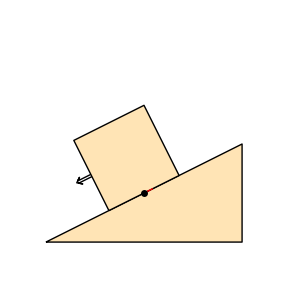

```mathematica
Figure[FigurePanel[
{

(* set styling *)
SetOptions[FigObject,FillColor->Moccasin],

(* inclined plane *)
FigPolygon⟦"wedge"⟧[
{{0,0},{1,0.5},{1,0}}
];

(* let us give the contact point a name *)
(* we do not strictly need to do this intermediate step, but it lets us also put a marker on the anchor for explanatory purposes *)
FigAnchor⟦"contactpt"⟧["wedge",Center,{1,0.5}];
(* here's that contact point, and its tangent orientation *)
FigAnchorMarker["contactpt",Layer->5];  (* use Layer so marker is not hidden by the rectangle we are about to draw *)

(* draw block translated and rotated, so side lies against contact point *)
FigRectangle⟦"block"⟧["contactpt",Radius->{0.2,0.2},AnchorOffset->Bottom,Rotate->Automatic],

(* now use anchors to make an arrow aligned with the block *)
FigArrow[{FigAnchor["block",Left],FromTail[-20]},ArrowType->"DoubleLine",Width->3,FillColor->None];

},
Frame->False,
PlotRange->{{0,1},{0,1}},ExtendRange->0.1
],
CanvasSize->{4,4},CanvasMargin->0
]
```